# CEPC Higgs Precision

(Dated: Sep. 11th,2015)
(Updated: Sep. 2017 for CEPC CDR）
(Updated: Oct. 2017 for CEPC CDR, with covariance matrix)
This code is used to determine projected Higgs precision achievable at Circular-Elector-Positron-Collider. 

A proper definition of projected precision has many physical requirements and can be defined in several different ways. The definition of precision on each parameter is using profiled-likelihood. Technically the definition is as follows, 
a) define a likelihood function;
a.a) here we take the probability P as -2Log[P]=χ^2 up to proper normalization;
a.b) χ^2 is defined as sum of (obs.-exp.)^2/(σ^2)_(Obs.), where obs. and exp. stands for observed and expected quantity and σ stands for the standard deviation;
b) find the allowed 1-sigma regions for a (set of) given parameter(s) κ(s);
b.a) this is equivalent to finding the largest range of  κ(s) that follow Δχ^2=χ^2-χ_min^2≤1;
b.b) “profiled” means while attempting to find such range, all the other parameters are allowed to vary freely within physical boundaries to minimize Δχ^2.
This program uses very simple linear regression method in finding such intervals. The efficiency of such algorithm decreases drastically for constrained fits with complex boundary conditions.

This fitting provides us guidance in prioritizing channels to study for the purpose of precision Higgs physics. Such guidance is indirect, only reveals itself via studying. 

Please consult Zhen Liu (zliu2@fnal.gov) for detailed explanation.

## PreCDR

## SM input

Branching ratios of the SM Higgs, 
assuming 125 GeV and reading from LHC Higgs cross section work group (cern twiki page).

```mathematica
brb=0.578;brtau=0.0637;brmu=2.21 10^-4;brs=4.4 10^-4;brc=2.68 10^-2;brg=8.56 10^-2;brgamma=2.30 10^-3;brw=0.216;brz=0.0267;
```

Higgs total width definition, only used when doing constrained fits where Higgs width is a derived quantity from other fitting parameters.

```mathematica
kh[kz_,kw_,kg_,kgamma_,kb_,kt_,ktau_]:=kb^2 brb+kw^2 brw+kz^2 brz+ktau^2 brtau+kg^2 brg+kgamma^2 brgamma+kt^2 brc+kb^2 brs+ktau^2 brmu+(1-brb-brw-brz-brtau-brg-brgamma-brc-brs-brmu);
```

Note: above branching fractions do not sum up to be exactly one, its up to the user to add the last piece

```mathematica
kh[1,1,1,1,1,1,1]
```

1.

## CEPC

This is the CEPC fitting program.
For simplicity, I removed many other components involving interfacing with HL-LHC/ILC measurements, other tested fits, etc.

7p and 10p stands for 7-parameter and 10-parameter;
“MD” stands for Model-dependent;
“MI” stands for Model-Independent.

In Prep subsections of both, 
Function_higgsobscepc  defines the processes to be measured at CEPC as a function of model parameters.
Table_higgsprecepc deines the projected precisions on these observables at CEPC.
Function_chisquarecepc defines the χ^2 function used to determine the precisions.

In 7p/10p_Fit_CEPC section, the fitting parameters are defined as in the list of
“arglist”.
As the projected precisions for CEPC measurements are for 5 ab^-1, others are deried by applying luminosity factors in the list “lumi, {xx,...}”, corresponding to luminosity of 5/xx ab^-1.

The results are simply shown in the last matrix in each section.
The rows are corresponding fitting parameters in the “arglsit”;
The columns are different luminosities, currently 0.5, 2, 5, 10 ab^-1;
In each parenthesis, the positive and negative are the allowed interval for the given parameter from their SM expected values.

### 7p_MD_Fits

#### Prep

```mathematica
higgsobscepc[kz_,kw_,kg_,kgamma_,kb_,kt_,ktau_]:={kz^2,kz^2 kb^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kt^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kg^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kw^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 ktau^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^4/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kgamma^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 ktau^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kw^2 kb^2/kh[kz,kw,kg,kgamma,kb,kt,ktau]};
higgsprecepc={0.51/100,0.28/100,2.2/100,1.6/100,1.5/100,1.2/100,4.3/100,9.0/100,17/100,2.8/100};
chisquarecepc[{kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_},lumif_]:=Sum[(higgsobscepc[kz,kw,kg,kgamma,kb,kt,ktau][[i]]-1)^2/higgsprecepc[[i]]^2/lumif,{i,1,Length[higgsprecepc]}]
```

#### 7p_fit_CEPC

```mathematica
dlistp=Table[RandomReal[]/20,{i,1,7}];
dlistm=Table[-RandomReal[]/20,{i,1,7}];
arglist={kb,kt,kg,kw,ktau,kz,kgamma};
cepc7p=Parallelize[Table[{tmparg=0;chi2t=0;While[chi2=NMinimize[inputlist=ReplacePart[arglist,i->1+dlistp[[i]]];{chisquarecepc[inputlist,lumif],kg> 0,kg<2,kgamma>0,kgamma<2,kb> 0,kb<2,kt> 0,kt<2,ktau> 0,ktau<2, kz<2, kz>0, kw<2, kw>0},{kz,kg,kgamma,kw,kb,kt,ktau}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistp[[i]]+(dlistp[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistp[[i]];dlistp[[i]]=tmparg2;chi2t=chi2];dlistp[[i]],
tmparg=0;chi2t=0;While[chi2=NMinimize[inputlist=ReplacePart[arglist,i->1+dlistm[[i]]];{chisquarecepc[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0},{kz,kg,kgamma,kw,kb,kt,ktau}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistm[[i]]+(dlistm[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistm[[i]];dlistm[[i]]=tmparg2;chi2t=chi2];dlistm[[i]]},{i,1,7},{lumif,{1}}],Method->"FinestGrained"];
```

```mathematica
cepc7p//MatrixForm
```

((0.0116166
-0.0119323)
(0.016217
-0.0164475)
(0.0146181
-0.0147799)
(0.0119357
-0.0121041)
(0.0132451
-0.0134957)
(0.00153721
-0.00168339)
(0.0456702
-0.0476205))

```mathematica
SetAccuracy[{{kb,kc,kg,kw,ktau,kz,kgamma},%67,%72,%83,%91},8]ᵀ//MatrixForm
```

(kb | {{0.0116166,-0.0119323}} | {{0.0116166,-0.0119323}} | {{0.0116166,-0.0119323}} | {{0.0116166,-0.0119323}}
kc | {{0.016217,-0.0164475}} | {{0.016217,-0.0164475}} | {{0.016217,-0.0164475}} | {{0.016217,-0.0164475}}
kg | {{0.0146182,-0.0147799}} | {{0.0146182,-0.0147799}} | {{0.0146182,-0.0147799}} | {{0.0146182,-0.0147799}}
kw | {{0.0119357,-0.012104}} | {{0.0119357,-0.0121041}} | {{0.0119357,-0.0121041}} | {{0.0119357,-0.0121041}}
ktau | {{0.0132451,-0.0134957}} | {{0.0132451,-0.0134957}} | {{0.0132451,-0.0134957}} | {{0.0132451,-0.0134957}}
kz | {{0.0015372,-0.0016834}} | {{0.0015372,-0.0016834}} | {{0.0015372,-0.0016834}} | {{0.0015372,-0.0016834}}
kgamma | {{0.0456702,-0.0476205}} | {{0.0456702,-0.0476205}} | {{0.04567,-0.0476205}} | {{0.0456702,-0.0476205}})

```mathematica
Table[D[chisquarecepc[{kb,kt,kg,kw,ktau,kz,kgamma},1],{kz,kw,kgamma,ktau,kg,kt,kb}[[i]],{kz,kw,kgamma,ktau,kg,kt,kb}[[j]]]/.{kb->1,kt->1,kg->1,kw->1,ktau->1,kz->1,kgamma->1},{i,1,7},{j,1,7}]
```

(1.42449×10^6 | -211647. | -1657.54 | -18420.3 | -67053.8 | -14423.9 | 334803.
-211647. | 80873.4 | 265.739 | 1248.59 | 11081. | 2010.95 | -92077.9
-1657.54 | 265.739 | 989.599 | -18.7214 | 75.1166 | 7.98936 | -1378.92
-18420.3 | 1248.59 | -18.7214 | 53520.4 | -344.352 | -539.374 | -54756.5
-67053.8 | 11081. | 75.1166 | -344.352 | 34524.2 | 445.096 | -48130.7
-14423.9 | 2010.95 | 7.98936 | -539.374 | 445.096 | 16493.5 | -18974.3
334803. | -92077.9 | -1378.92 | -54756.5 | -48130.7 | -18974.3 | 231454.)

```mathematica
Table[D[chisquarecepc[{kb,kt,kg,kw,ktau,kz,kgamma},1],{kz,kw,kgamma,ktau,kg,kt,kb}[[i]],{kz,kw,kgamma,ktau,kg,kt,kb}[[j]]]*If[i==j,1,0]/.{kb->1,kt->1,kg->1,kw->1,ktau->1,kz->1,kgamma->1},{i,1,7},{j,1,7}]
```

(1.42449×10^6 | 0 | 0 | 0 | 0 | 0 | 0
0 | 80873.4 | 0 | 0 | 0 | 0 | 0
0 | 0 | 989.599 | 0 | 0 | 0 | 0
0 | 0 | 0 | 53520.4 | 0 | 0 | 0
0 | 0 | 0 | 0 | 34524.2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 16493.5 | 0
0 | 0 | 0 | 0 | 0 | 0 | 231454.)

```mathematica
Inverse[%39]^0.5.%38.Inverse[%39]^0.5
```

(1. | -0.623564 | -0.0441473 | -0.0667125 | -0.302366 | -0.0941015 | 0.583079
-0.623564 | 1. | 0.0297045 | 0.0189784 | 0.209707 | 0.0550608 | -0.673008
-0.0441473 | 0.0297045 | 1. | -0.00257246 | 0.0128512 | 0.00197754 | -0.0911123
-0.0667125 | 0.0189784 | -0.00257246 | 1. | -0.0080109 | -0.0181541 | -0.491976
-0.302366 | 0.209707 | 0.0128512 | -0.0080109 | 1. | 0.0186525 | -0.538429
-0.0941015 | 0.0550608 | 0.00197754 | -0.0181541 | 0.0186525 | 1. | -0.307099
0.583079 | -0.673008 | -0.0911123 | -0.491976 | -0.538429 | -0.307099 | 1.)

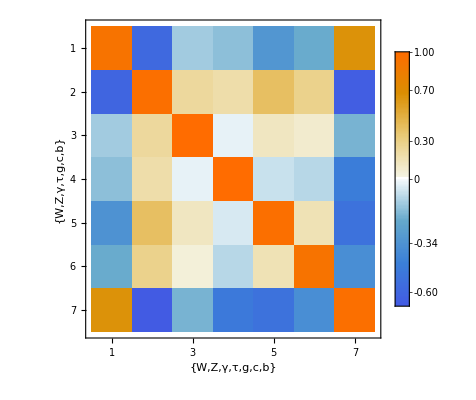

```mathematica
MatrixPlot[%40,FrameLabel->{{"W","Z","γ","τ","g","c","b"},{"W","Z","γ","τ","g","c","b"}},PlotLegends->Automatic]
```

```mathematica
Eigenvalues[%21]
```

{1.45764×10^6,221226.,67099.7,48535.6,30937.8,15919.6,987.163}

### 10p_MI_Fits

#### Prep

```mathematica
higgsobscepc[kz_,kw_,kg_,kgamma_,kb_,kt_,ktau_,kmu_,brinv_,ktotal_]:={kz^2,kz^2 kb^2/ktotal,kz^2 kt^2/ktotal,kz^2 kg^2/ktotal,kz^2 kw^2/ktotal,kz^2 ktau^2/ktotal,kz^4/ktotal,kz^2 kgamma^2/ktotal,kz^2 kmu^2/ktotal,kw^2 kb^2/ktotal,kz^2brinv+1};
higgsprecepc={0.51/100,0.28/100,2.2/100,1.6/100,1.5/100,1.2/100,4.3/100,9.0/100,17/100,2.8/100,0.14/100};
chisquarecepc[{kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_,kmu_,brinv_,ktotal_},lumif_]:=Sum[(higgsobscepc[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[i]]-1)^2/higgsprecepc[[i]]^2/lumif,{i,1,Length[higgsprecepc]}]
```

#### 10p_fit_CEPC

```mathematica
dlistp=Table[RandomReal[]/20,{i,1,10}];
dlistm=Table[-RandomReal[]/20,{i,1,10}];
arglist={kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal};
cepc10p=Parallelize[Table[{tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠9,inputlist=ReplacePart[arglist,i->1+dlistp[[i]]],inputlist=ReplacePart[arglist,i->dlistp[[i]]]];{chisquarecepc[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<2,kmu≥ 0, kmu<2,ktotal>0, ktotal≤2},{kz,kg,kgamma,kw,kb,kt,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistp[[i]]+(dlistp[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistp[[i]];dlistp[[i]]=tmparg2;chi2t=chi2];dlistp[[i]],
tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠ 9,inputlist=ReplacePart[arglist,i->1+dlistm[[i]]],inputlist=ReplacePart[arglist,i->dlistm[[i]]]];{chisquarecepc[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<2,kmu≥ 0, kmu<2,ktotal>0, ktotal≤2},{kz,kg,kgamma,kw,kb,kt,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistm[[i]]+(dlistm[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistm[[i]];dlistm[[i]]=tmparg2;chi2t=chi2];dlistm[[i]]},{i,1,10},{lumif,{10,2.5,1,0.5}}],Method->"FinestGrained"];
cepc10p//MatrixForm
```

((0.0420525
-0.0403854) | (0.0208194
-0.0204033) | (0.0131192
-0.0129528) | (0.00925944
-0.00917626)
(0.0549682
-0.0530561) | (0.0272377
-0.0267595) | (0.0171701
-0.0169788) | (0.012121
-0.0120254)
(0.0494335
-0.0474334) | (0.0244641
-0.0239643) | (0.015414
-0.0152141) | (0.0108786
-0.0107786)
(0.0387409
-0.0385975) | (0.0193637
-0.0193283) | (0.012244
-0.0122299) | (0.00865667
-0.00864962)
(0.0464184
-0.0444732) | (0.0229652
-0.0224792) | (0.0144679
-0.0142735) | (0.0102101
-0.010113)
(0.00803156
-0.00809659) | (0.00402379
-0.00404005) | (0.00254676
-0.00255326) | (0.0018015
-0.00180475)
(0.14182
-0.157784) | (0.0723428
-0.0762269) | (0.0461336
-0.0476789) | (0.0327644
-0.0335357)
(0.245948
-0.320985) | (0.128651
-0.145883) | (0.082924
-0.0897124) | (0.0592333
-0.0626106)
(0.00442776
-0.00442774) | (0.00221367
-0.00221367) | (0.00140002
-0.00140002) | (0.000989956
-0.000989956)
(0.0910399
-0.0834866) | (0.0445451
-0.0426581) | (0.0279496
-0.0271949) | (0.0196843
-0.019307))

## CDR

### SM input

Branching ratios of the SM Higgs, 
assuming 125 GeV and reading from LHC Higgs cross section work group (cern twiki page).

```mathematica
brb=0.578;brtau=0.0637;brmu=2.21 10^-4;brs=4.4 10^-4;brc=2.68 10^-2;brg=8.56 10^-2;brgamma=2.30 10^-3;brw=0.216;brz=0.0267;
```

Higgs total width definition, only used when doing constrained fits where Higgs width is a derived quantity from other fitting parameters.

```mathematica
kh[kz_,kw_,kg_,kgamma_,kb_,kt_,ktau_]:=kb^2 brb+kw^2 brw+kz^2 brz+ktau^2 brtau+kg^2 brg+kgamma^2 brgamma+kt^2 brc+kb^2 brs+ktau^2 brmu+(1-brb-brw-brz-brtau-brg-brgamma-brc-brs-brmu);
```

Note: above branching fractions do not sum up to be exactly one, its up to the user to add the last piece

```mathematica
kh[1,1,1,1,1,1,1]
```

1.

### Prep (input)

```mathematica
(*higgsobscepc[kz_,kw_,kg_,kgamma_,kb_,kt_,ktau_]:={kz^2 ktau^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 ktau^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kgamma^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kw^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^4/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kg^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kt^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kb^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kw^2 kb^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],6/7 kz^2 kb^2/kh[kz,kw,kg,kgamma,kb,kt,ktau]+1/7 kw^2 kb^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2};
higgsprecepc={(0.149731+0.158474)*100/2,(0.0133717+0.0133935)*100/2,(0.0807207+0.0820905)*100/2,(0.0126807+0.0128432)*100/2,(0.049666+0.0509421)*100/2,(0.0144769+0.0144958)*100/2,(0.0352087+0.035472)*100/2,(0.00326826+0.00326885)*100/2,(0.0311003+0.0312155)*100/2,(0.00472532+0.00472881)*100/2,(0.00498383+0.00500063)*100/2}/100;
higgsprecepc={15.9,0.888,8.32,1.03,5.07,1.42,3.55,(0.00326191+0.00326551)*100/2,(0.0311003+0.0312155)*100/2,Infinity(*(0.00401209+0.00402172)*100/2*),0.5}/100;
inputcorrelations=(*Nov.6.2017*){{100,-0.475,-0.086,-0.365,-0.164,-0.046,0.018,-0.002,0.004,0},{-0.475,100,-1.115,-5.857,-2.343,0.454,0.133,0.005,-0.011,0},{-0.086,-1.115,100,-0.918,-0.398,0.093,0.017,-0.005,0.011,0},{-0.365,-5.857,-0.918,100,-6.530,-8.025,-5.704,-0.031,0.074,0},{-0.164,-2.343,-0.398,-6.530,100,-1.793,-1.380,0.588,-1.379,0},{-0.046,0.454,0.093,-8.025,-1.793,100,-15.768,-0.290,0.679,0},{0.018,0.133,0.017,-5.704,-1.380,-15.768,100,4.446,-10.425,0},{-0.002,0.005,-0.005,-0.031,0.588,-0.290,4.446,100,-42.653,0},{0.004,-0.011,0.011,0.074,-1.379,0.679,-10.425,-42.653,100,0},{0,0,0,0,0,0,0,0,0,100}};
inputcorrelations=(*Jan.7.2018*){{100,-2.58,-0.29,-0.58,-0.16,0.40,-0.68,0.14,-0.06,0.09,0},{-2.58,100,-6.14,-18.57,-6.47,9.50,-5.36,3.45,-1.58,-0.51,0},{-0.29,-6.14,100,0.33,-0.38,0.08,-0.63,0.06,-0.03,0.14,0},{-0.58,-18.57,0.33,100,-16.34,-33.83,-13.56,-8.42,3.87,1.10,0},{-0.16,-6.47,-0.38,-16.34,100,-10.85,-6.65,-11.85,5.44,-4.15,0},{0.40,9.50,0.08,-33.83,-10.85,100,-16.72,-6.77,3.11,-1.05,0},{-0.68,-5.36,-0.63,-13.56,-6.65,-16.72,100,-4.13,1.90,-6.20,0},{0.14,3.45,0.06,-8.42,-11.85,-6.77,-4.13,100,-45.91,1.35,0},
{-0.06,-1.58,-0.03,3.87,5.44,3.11,1.90,-45.91,100,-0.62,0},{0.09,-0.51,0.14,1.10,-4.15,-1.05,-6.20,1.35,-0.62,100,0},{0,0,0,0,0,0,0,0,0,0,100}};
halfcorrelation=(*Apr.15.2018*)SparseArray[{{11,11}->0,{4,2}->-22.661,{5,2}->-14.181,{6,2}->9.214,{7,2}->2.329,{8,2}->4.237,{9,2}->-1.974,{10,2}->0.257,{5,4}->-12.487,{6,4}->-27.633,{7,4}->-10.609,{8,4}->-7.886,{9,4}->3.675,{10,4}->1.658,{6,5}->-13.483,{7,5}->-6.800,{8,5}->-12.420,{9,5}->5.788,{10,5}->-4.351,{7,6}->-19.209,{8,6}->-7.648,{9,6}-> 3.564,{10,6}->-1.081,{8,7}-> -4.463,{9,7}-> 2.080,{10,7}-> -6.389,{9,8}-> -46.606,{10,8}-> 1.335,{10,9}-> -0.622}]//Normal;
inputcorrelations=(*Apr.15.2018*)IdentityMatrix[11]*100+halfcorrelationᵀ+halfcorrelation;
(*chisquarecepc[{kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_},lumif_]:=Sum[If[i==j,((higgsobscepc[kz,kw,kg,kgamma,kb,kt,ktau][[i]]-1)/higgsprecepc[[i]])((higgsobscepc[kz,kw,kg,kgamma,kb,kt,ktau][[j]]-1)/higgsprecepc[[j]])/lumif,0],{i,1,Length[higgsprecepc]},{j,1,Length[higgsprecepc]}]*)*)
```

### Defining χ^2 s

```mathematica
chisquarecepc[{kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_},lumif_]:=Sum[((higgsobscepc[kz,kw,kg,kgamma,kb,kt,ktau][[i]]-1)/higgsprecepc[[i]])((higgsobscepc[kz,kw,kg,kgamma,kb,kt,ktau][[j]]-1)/higgsprecepc[[j]])inputcorrelations[[i,j]]/100/lumif,{i,1,Length[higgsprecepc]},{j,1,Length[higgsprecepc]}]
higgsobsLHCratios[kz_,kw_,kg_,kgamma_,kb_,kt_,ktau_]:={kg^2 kz^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kgamma/kz,kw/kz,kb/kz,ktau/kz,kg/kz,kt/kg,ktau/kz};
higgspreLHCratiosL={2.0/100,1.8/100,2.1/100,7.4/100,7.8/100,4.5/100,5.0/100,6.1/100};
(*higgspreLHCratiosH={5.7/100,2.6/100,3.1/100,9.8/100,8.9/100,8.7/100,8/100,9.4/100,6.3/100};*)
chisquarecepcL[{kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_},lumif_]:=Sum[((higgsobscepc[kz,kw,kg,kgamma,kb,kt,ktau][[i]]-1)/higgsprecepc[[i]])((higgsobscepc[kz,kw,kg,kgamma,kb,kt,ktau][[j]]-1)/higgsprecepc[[j]])inputcorrelations[[i,j]]/100/lumif,{i,1,Length[higgsprecepc]},{j,1,Length[higgsprecepc]}]+Sum[(higgsobsLHCratios[kz,kw,kg,kgamma,kb,kt,ktau][[i]]-1)^2/higgspreLHCratiosL[[i]]^2,{i,1,Length[higgspreLHCratiosL]}]
```

```mathematica
higgsobscepc10p[kz_,kw_,kg_,kgamma_,kb_,kt_,ktau_,kmu_,brinv_,ktotal_]:={kz^2 kmu^2/ktotal,kz^2 ktau^2/ktotal,kz^2 kgamma^2/ktotal,kz^2 kw^2/ktotal,kz^4/ktotal,kz^2 kg^2/ktotal,kz^2 kt^2/ktotal,kz^2 kb^2/ktotal,kw^2 kb^2/ktotal,6/7 kz^2 kb^2/ktotal+1/7 kw^2 kb^2/ktotal,kz^2,kz^2brinv+1};
chisquarecepc10p[{kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_,kmu_,brinv_,ktotal_},lumif_]:=Sum[((higgsobscepc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[i]]-1)/higgsprecepc[[i]])((higgsobscepc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[j]]-1)/higgsprecepc[[j]])inputcorrelations[[i,j]]/100/lumif,{i,1,Length[higgsprecepc]},{j,1,Length[higgsprecepc]}]+(higgsobscepc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[-1]]-1)^2/higgsobscepcinv^2
higgsobsLHCratios10p[kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_,kmu_,brinv_,ktotal_]:={kg^2 kz^2/ktotal,kgamma/kz,kw/kz,kb/kz,ktau/kz,kg/kz,kt/kg,kmu/kz};
chisquarecepc10pL[{kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_,kmu_,brinv_,ktotal_},lumif_]:=Sum[((higgsobscepc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[i]]-1)/higgsprecepc[[i]])((higgsobscepc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[j]]-1)/higgsprecepc[[j]])inputcorrelations[[i,j]]/100/lumif,{i,1,Length[higgsprecepc]},{j,1,Length[higgsprecepc]}]+(higgsobscepc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[-1]]-1)^2/higgsobscepcinv^2+Sum[(higgsobsLHCratios10p[kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal][[i]]-1)^2/higgspreLHCratiosL[[i]]^2,{i,1,Length[higgspreLHCratiosL]}]
```

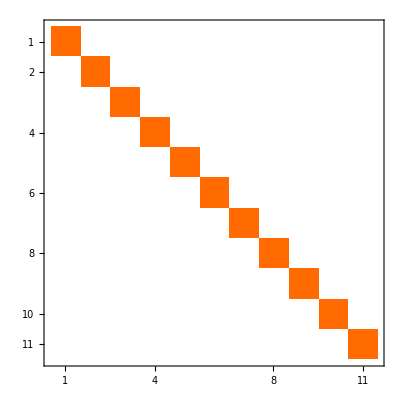

```mathematica
MatrixPlot[inputcorrelations]
```

```mathematica
inputcorrelations//MatrixForm
```

(100 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 100 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 100 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 100 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 100 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 100 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 100 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 100 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 100 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 100 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 100)

```mathematica
inputcorrelations-inputcorrelationsᵀ//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

### 7p_fit_CEPC

```mathematica
dlistp=Table[RandomReal[]/20,{i,1,7}];
dlistm=Table[-RandomReal[]/20,{i,1,7}];
arglist={kb,kt,kg,kw,ktau,kz,kgamma};
cepc7p=Parallelize[Table[{tmparg=0;chi2t=0;While[chi2=NMinimize[inputlist=ReplacePart[arglist,i->1+dlistp[[i]]];{chisquarecepc[inputlist,lumif],kg> 0,kg<2,kgamma>0,kgamma<2,kb> 0,kb<2,kt> 0,kt<2,ktau> 0,ktau<2, kz<2, kz>0, kw<2, kw>0},{kz,kg,kgamma,kw,kb,kt,ktau}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistp[[i]]+(dlistp[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistp[[i]];dlistp[[i]]=tmparg2;chi2t=chi2];dlistp[[i]],
tmparg=0;chi2t=0;While[chi2=NMinimize[inputlist=ReplacePart[arglist,i->1+dlistm[[i]]];{chisquarecepc[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0},{kz,kg,kgamma,kw,kb,kt,ktau}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistm[[i]]+(dlistm[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistm[[i]];dlistm[[i]]=tmparg2;chi2t=chi2];dlistm[[i]]},{i,1,7},{lumif,{1}}],Method->"FinestGrained"];
```

```mathematica
cepc7p//MatrixForm
```

((0.0151823
-0.0150728)
(0.0223004
-0.0221779)
(0.0160248
-0.0158907)
(0.0137905
-0.0137686)
(0.014734
-0.0146334)
(0.00151904
-0.00152118)
(0.0368909
-0.0375193))

```mathematica
SetAccuracy[{{kb,kc,kg,kw,ktau,kz,kgamma},cepc7p*100},3]ᵀ//MatrixForm
```

(kb | {{1.52,-1.51}}
kc | {{2.23,-2.22}}
kg | {{1.6,-1.59}}
kw | {{1.38,-1.38}}
ktau | {{1.47,-1.46}}
kz | {{0.15,-0.15}}
kgamma | {{3.69,-3.75}})

```mathematica
covariancematrix7p=Table[D[chisquarecepc[{kb,kt,kg,kw,ktau,kz,kgamma},1],{kb,kt,kg,kw,ktau,kz,kgamma}[[i]],{kb,kt,kg,kw,ktau,kz,kgamma}[[j]]]/.{kb->1,kt->1,kg->1,kw->1,ktau->1,kz->1,kgamma->1},{i,1,7},{j,1,7}]
```

{{221281.,-8709.93,-53522.8,-94432.6,-73336.3,220341.,-1472.31},{-8709.93,8297.05,-2758.06,4306.24,-848.706,-27105.9,15.8073},{-53522.8,-2758.06,53384.2,9407.06,-4211.95,-64149.7,-4.13634},{-94432.6,4306.24,9407.06,121450.,-26644.3,-182731.,18.4035},{-73336.3,-848.706,-4211.95,-26644.3,109738.,40259.,-212.186},{220341.,-27105.9,-64149.7,-182731.,40259.,1.26557×10^6,-478.144},{-1472.31,15.8073,-4.13634,18.4035,-212.186,-478.144,1706.97}}

```mathematica
correlationmatrix7p=Inverse[Sqrt[Diagonal[covariancematrix7p]]IdentityMatrix[7]].covariancematrix7p.Inverse[Sqrt[Diagonal[covariancematrix7p]]IdentityMatrix[7]]
```

{{1.,-0.203273,-0.492448,-0.576038,-0.470617,0.416369,-0.0757557},{-0.203273,1.,-0.13105,0.135656,-0.0281266,-0.26452,0.00420031},{-0.492448,-0.13105,1.,0.116829,-0.0550299,-0.2468,-0.000433308},{-0.576038,0.135656,0.116829,1.,-0.230796,-0.46609,0.00127817},{-0.470617,-0.0281266,-0.0550299,-0.230796,1.,0.108029,-0.0155033},{0.416369,-0.26452,-0.2468,-0.46609,0.108029,1.,-0.0102873},{-0.0757557,0.00420031,-0.000433308,0.00127817,-0.0155033,-0.0102873,1.}}

### 7p_fit_CEPC_LHC

```mathematica
dlistp=Table[RandomReal[]/20,{i,1,7}];
dlistm=Table[-RandomReal[]/20,{i,1,7}];
arglist={kb,kt,kg,kw,ktau,kz,kgamma};
cepc7pL=Parallelize[Table[{tmparg=0;chi2t=0;While[chi2=NMinimize[inputlist=ReplacePart[arglist,i->1+dlistp[[i]]];{chisquarecepcL[inputlist,lumif],kg> 0,kg<2,kgamma>0,kgamma<2,kb> 0,kb<2,kt> 0,kt<2,ktau> 0,ktau<2, kz<2, kz>0, kw<2, kw>0},{kz,kg,kgamma,kw,kb,kt,ktau}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistp[[i]]+(dlistp[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistp[[i]];dlistp[[i]]=tmparg2;chi2t=chi2];dlistp[[i]],
tmparg=0;chi2t=0;While[chi2=NMinimize[inputlist=ReplacePart[arglist,i->1+dlistm[[i]]];{chisquarecepcL[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0},{kz,kg,kgamma,kw,kb,kt,ktau}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistm[[i]]+(dlistm[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistm[[i]];dlistm[[i]]=tmparg2;chi2t=chi2];dlistm[[i]]},{i,1,7},{lumif,{1}}],Method->"FinestGrained"];
```

```mathematica
SetAccuracy[{{kb,kc,kg,kw,ktau,kz,kgamma},cepc7p*100,cepc7pL*100},3]ᵀ//MatrixForm
```

(kb | {{1.52,-1.51}} | {{1.15,-1.14}}
kc | {{2.23,-2.22}} | {{1.94,-1.93}}
kg | {{1.6,-1.59}} | {{1.22,-1.21}}
kw | {{1.38,-1.38}} | {{1.05,-1.05}}
ktau | {{1.47,-1.46}} | {{1.13,-1.12}}
kz | {{0.15,-0.15}} | {{0.15,-0.15}}
kgamma | {{3.69,-3.75}} | {{1.61,-1.62}})

```mathematica
SetAccuracy[{{kb,kc,kg,kw,ktau,kz,kgamma},Abs[cepc7p]*100,Abs[cepc7pL]*100},2]ᵀ//MatrixForm
```

(kb | {{1.5,1.5}} | {{1.1,1.1}}
kc | {{2.2,2.2}} | {{1.9,1.9}}
kg | {{1.6,1.6}} | {{1.2,1.2}}
kw | {{1.4,1.4}} | {{1.,1.}}
ktau | {{1.5,1.5}} | {{1.1,1.1}}
kz | {{0.2,0.2}} | {{0.1,0.1}}
kgamma | {{3.7,3.8}} | {{1.6,1.6}})

```mathematica
SetAccuracy[{{kb,kc,kg,kw,ktau,kz,kgamma},cepc7pL*100},3]ᵀ//MatrixForm
```

(kb | {{1.15,-1.14}}
kc | {{1.94,-1.93}}
kg | {{1.22,-1.21}}
kw | {{1.05,-1.05}}
ktau | {{1.13,-1.12}}
kz | {{0.15,-0.15}}
kgamma | {{1.61,-1.62}})

```mathematica
covariancematrix7pL=Table[D[chisquarecepcL[{kb,kt,kg,kw,ktau,kz,kgamma},1],{kb,kt,kg,kw,ktau,kz,kgamma}[[i]],{kb,kt,kg,kw,ktau,kz,kgamma}[[j]]]/.{kb->1,kt->1,kg->1,kw->1,ktau->1,kz->1,kgamma->1},{i,1,7},{j,1,7}]
```

{{228338.,-8399.88,-64101.4,-91933.7,-72596.8,208715.,-1445.71},{-8399.88,9111.41,-4048.18,4422.02,-814.444,-27627.6,17.0401},{-64101.4,-4048.18,71894.4,5456.85,-5380.94,-47337.6,-46.1987},{-91933.7,4422.02,5456.85,126918.,-26368.2,-191471.,28.3395},{-72596.8,-814.444,-5380.94,-26368.2,110686.,38148.5,-209.246},{208715.,-27627.6,-47337.6,-191471.,38148.5,1.29745×10^6,-6695.76},{-1445.71,17.0401,-46.1987,28.3395,-209.246,-6695.76,7879.92}}

```mathematica
correlationmatrix7pL=Inverse[Sqrt[Diagonal[covariancematrix7pL]]IdentityMatrix[7]].covariancematrix7pL.Inverse[Sqrt[Diagonal[covariancematrix7pL]]IdentityMatrix[7]]
```

{{1.,-0.184158,-0.5003,-0.540037,-0.456648,0.38346,-0.0340824},{-0.184158,1.,-0.158168,0.130037,-0.0256461,-0.2541,0.00201102},{-0.5003,-0.158168,1.,0.0571259,-0.0603204,-0.154994,-0.00194098},{-0.540037,0.130037,0.0571259,1.,-0.222471,-0.471841,0.000896126},{-0.456648,-0.0256461,-0.0603204,-0.222471,1.,0.100667,-0.00708515},{0.38346,-0.2541,-0.154994,-0.471841,0.100667,1.,-0.0662207},{-0.0340824,0.00201102,-0.00194098,0.000896126,-0.00708515,-0.0662207,1.}}

### 10p-fit-CEPC

```mathematica
dlistp=Table[RandomReal[]/20,{i,1,10}];
dlistm=Table[-RandomReal[]/20,{i,1,10}];
arglist={kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal};
cepc10p=Parallelize[Table[{tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠9,inputlist=ReplacePart[arglist,i->1+dlistp[[i]]],inputlist=ReplacePart[arglist,i->dlistp[[i]]]];{chisquarecepc10p[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<1,kmu≥ 0, kmu<2,ktotal>0, ktotal≤2},{kz,kg,kgamma,kw,kb,kt,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistp[[i]]+(dlistp[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistp[[i]];dlistp[[i]]=tmparg2;chi2t=chi2];dlistp[[i]],
tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠ 9,inputlist=ReplacePart[arglist,i->1+dlistm[[i]]],inputlist=ReplacePart[arglist,i->dlistm[[i]]]];{chisquarecepc10p[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<1,kmu≥ 0, kmu<2,ktotal>0, ktotal≤2},{kz,kg,kgamma,kw,kb,kt,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistm[[i]]+(dlistm[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistm[[i]];dlistm[[i]]=tmparg2;chi2t=chi2];dlistm[[i]]},{i,1,10},{lumif,{1}}],Method->"FinestGrained"];
cepc10p//MatrixForm
```

```mathematica
SetAccuracy[{{kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal},cepc10p*100},3]ᵀ//MatrixForm
```

(kb | {{1.52,-1.51}}
kt | {{2.14,-2.13}}
kg | {{1.57,-1.56}}
kw | {{1.34,-1.34}}
ktau | {{1.49,-1.48}}
kz | {{0.25,-0.25}}
kgamma | {{3.4,-3.44}}
kmu | {{7.96,-8.56}}
brinv | {{0.16,-0.16}}
ktotal | {{3.09,-3.02}})

```mathematica
covariancematrix10p=Table[D[chisquarecepc10p[{kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal},1],{kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal}[[i]],{kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal}[[j]]]/.{kb->1,kt->1,kg->1,kw->1,ktau->1,kz->1,kgamma->1,kmu->1,brinv->0,ktotal->1},{i,1,10},{j,1,10}];
```

```mathematica
Inverse[Sqrt[Diagonal[covariancematrix10p]]IdentityMatrix[10]]
```

{{0.00111088,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.0109602,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.004278,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.00316331,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.00279307,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.000856895,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.0218142,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.0572756,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.00110245,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00202191}}

```mathematica
correlationmatrix10p=Inverse[Sqrt[Diagonal[covariancematrix10p]]IdentityMatrix[10]].covariancematrix10p.Inverse[Sqrt[Diagonal[covariancematrix10p]]IdentityMatrix[10]]
```

{{1.,-0.0671361,-0.132342,-0.100698,0.000270184,0.771175,0.,0.,0.,-0.875158},{-0.0671361,1.,-0.23911,-0.0158737,0.00599,-0.0302845,0.,0.,0.,0.0319986},{-0.132342,-0.23911,1.,-0.0170747,0.00842,0.0657223,0.,0.,0.,-0.0844758},{-0.100698,-0.0158737,-0.0170747,1.,-0.120791,0.0695728,0.,0.,0.,-0.130404},{0.000270184,0.00599,0.00842,-0.120791,1.,0.269603,0.,0.,0.,-0.322105},{0.771175,-0.0302845,0.0657223,0.0695728,0.269603,1.,0.0392814,0.0149609,0.,-0.86951},{0.,0.,0.,0.,0.,0.0392814,1.,0.,0.,-0.0463437},{0.,0.,0.,0.,0.,0.0149609,0.,1.,0.,-0.0176507},{0.,0.,0.,0.,0.,0.,0.,0.,1.,0.},{-0.875158,0.0319986,-0.0844758,-0.130404,-0.322105,-0.86951,-0.0463437,-0.0176507,0.,1.}}

### 10p-fit-CEPC-LHC

```mathematica
dlistp=Table[RandomReal[]/20,{i,1,10}];
dlistm=Table[-RandomReal[]/20,{i,1,10}];
arglist={kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal};
cepc10pL=Parallelize[Table[{tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠9,inputlist=ReplacePart[arglist,i->1+dlistp[[i]]],inputlist=ReplacePart[arglist,i->dlistp[[i]]]];{chisquarecepc10pL[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<2,kmu≥ 0, kmu<2,ktotal>0, ktotal≤2},{kz,kg,kgamma,kw,kb,kt,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistp[[i]]+(dlistp[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistp[[i]];dlistp[[i]]=tmparg2;chi2t=chi2];dlistp[[i]],
tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠ 9,inputlist=ReplacePart[arglist,i->1+dlistm[[i]]],inputlist=ReplacePart[arglist,i->dlistm[[i]]]];{chisquarecepc10pL[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<2,kmu≥ 0, kmu<2,ktotal>0, ktotal≤2},{kz,kg,kgamma,kw,kb,kt,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistm[[i]]+(dlistm[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistm[[i]];dlistm[[i]]=tmparg2;chi2t=chi2];dlistm[[i]]},{i,1,10},{lumif,{1}}],Method->"FinestGrained"];
cepc10pL//MatrixForm
```

((0.0121778
-0.0120808)
(0.019464
-0.0194152)
(0.0126202
-0.0125179)
(0.010791
-0.0107601)
(0.012029
-0.0119349)
(0.00249688
-0.00250313)
(0.0163029
-0.0163208)
(0.0494969
-0.0502516)
(0.00174622
-0.00174622)
(0.0251311
-0.0246092))

```mathematica
SetAccuracy[{{kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal},cepc10p*100,cepc10pL*100},3]ᵀ//MatrixForm
```

(kb | {{1.58,-1.57}} | {{1.22,-1.21}}
kt | {{2.23,-2.22}} | {{1.95,-1.94}}
kg | {{1.63,-1.62}} | {{1.26,-1.25}}
kw | {{1.4,-1.4}} | {{1.08,-1.08}}
ktau | {{1.53,-1.52}} | {{1.2,-1.19}}
kz | {{0.25,-0.25}} | {{0.25,-0.25}}
kgamma | {{3.71,-3.77}} | {{1.63,-1.63}}
kmu | {{8.38,-9.05}} | {{4.95,-5.03}}
brinv | {{0.17,-0.17}} | {{0.17,-0.17}}
ktotal | {{3.18,-3.11}} | {{2.51,-2.46}})

```mathematica
SetAccuracy[{{kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal},cepc10p*100,cepc10pL*100},2]ᵀ//MatrixForm
```

(kb | 1.6 | 1.2
kt | 2.2 | 1.9
kg | 1.6 | 1.3
kw | 1.4 | 1.1
ktau | 1.5 | 1.2
kz | 0.3 | 0.3
kgamma | 3.7 | 1.6
kmu | 8.7 | 5.
brinv | 0.2 | 0.2
ktotal | 3.1 | 2.5)

```mathematica
covariancematrix10pL=Table[D[chisquarecepc10pL[{kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal},1],{kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal}[[i]],{kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal}[[j]]]/.{kb->1,kt->1,kg->1,kw->1,ktau->1,kz->1,kgamma->1,kmu->1,brinv->0,ktotal->1},{i,1,10},{j,1,10}];
```

```mathematica
correlationmatrix10pL=Inverse[Sqrt[Diagonal[covariancematrix10pL]]IdentityMatrix[10]].covariancematrix10pL.Inverse[Sqrt[Diagonal[covariancematrix10pL]]IdentityMatrix[10]]
```

{{1.,-0.0521054,-0.107699,-0.111759,0.000977994,0.761461,0.,0.,0.,-0.871264},{-0.0521054,1.,-0.220625,-0.0220666,0.00722526,-0.0206934,0.,0.,0.,0.0215454},{-0.107699,-0.220625,1.,-0.0146397,0.00806592,0.11301,0.,0.,0.,-0.144632},{-0.111759,-0.0220666,-0.0146397,1.,-0.13925,0.040994,0.,0.,0.,-0.10565},{0.000977994,0.00722526,0.00806592,-0.13925,1.,0.254204,0.,0.,0.,-0.308594},{0.761461,-0.0206934,0.11301,0.040994,0.254204,1.,-0.0432801,-0.00797848,0.,-0.863129},{0.,0.,0.,0.,0.,-0.0432801,1.,0.,0.,-0.0197757},{0.,0.,0.,0.,0.,-0.00797848,0.,1.,0.,-0.00986417},{0.,0.,0.,0.,0.,0.,0.,0.,1.,0.},{-0.871264,0.0215454,-0.144632,-0.10565,-0.308594,-0.863129,-0.0197757,-0.00986417,0.,1.}}

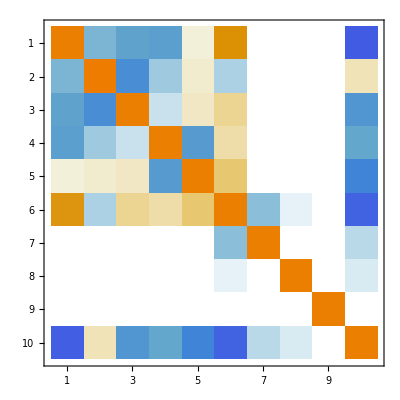

```mathematica
MatrixPlot[correlationmatrix10pL]
```

## CDR (width subchannel ZZ)

```mathematica
higgsprecepcoriginal=higgsprecepc
```

{0.171,0.0082,0.0684,0.0098,0.0509,0.0127,0.0326,0.003068,0.029991,∞,0.005}

```mathematica
higgsprecepc=Table[If[i==5||i==11,higgsprecepcoriginal[[i]],Infinity],{i,1,11}]
```

{∞,∞,∞,∞,0.0509,∞,∞,∞,∞,∞,0.005}

```mathematica
higgsobscepc[kz_,kw_,kg_,kgamma_,kb_,kt_,ktau_]:={kz^2 ktau^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 ktau^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kgamma^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kw^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^4/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kg^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kt^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kb^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kw^2 kb^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],6/7 kz^2 kb^2/kh[kz,kw,kg,kgamma,kb,kt,ktau]+1/7 kw^2 kb^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2};
higgsprecepc={Infinity,Infinity,Infinity,Infinity,5.07,Infinity,Infinity,Infinity,Infinity,Infinity,0.5}/100;
chisquarecepc[{kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_},lumif_]:=Sum[((higgsobscepc[kz,kw,kg,kgamma,kb,kt,ktau][[i]]-1)/higgsprecepc[[i]])((higgsobscepc[kz,kw,kg,kgamma,kb,kt,ktau][[j]]-1)/higgsprecepc[[j]])inputcorrelations[[i,j]]/100/lumif,{i,1,Length[higgsprecepc]},{j,1,Length[higgsprecepc]}]
higgsobsLHCratios[kz_,kw_,kg_,kgamma_,kb_,kt_,ktau_]:={kg^2 kz^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kgamma/kz,kw/kz,kb/kz,ktau/kz,kg/kz,kt/kg,ktau/kz};
higgspreLHCratiosL={2.0/100,1.8/100,2.1/100,7.4/100,7.8/100,4.5/100,5.0/100,6.1/100};
(*higgspreLHCratiosH={5.7/100,2.6/100,3.1/100,9.8/100,8.9/100,8.7/100,8/100,9.4/100,6.3/100};*)
chisquarecepcL[{kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_},lumif_]:=Sum[((higgsobscepc[kz,kw,kg,kgamma,kb,kt,ktau][[i]]-1)/higgsprecepc[[i]])((higgsobscepc[kz,kw,kg,kgamma,kb,kt,ktau][[j]]-1)/higgsprecepc[[j]])inputcorrelations[[i,j]]/100/lumif,{i,1,Length[higgsprecepc]},{j,1,Length[higgsprecepc]}]+Sum[(higgsobsLHCratios[kz,kw,kg,kgamma,kb,kt,ktau][[i]]-1)^2/higgspreLHCratiosL[[i]]^2,{i,1,Length[higgspreLHCratiosL]}]
```

```mathematica
higgsobscepc10p[kz_,kw_,kg_,kgamma_,kb_,kt_,ktau_,kmu_,brinv_,ktotal_]:={kz^2 kmu^2/ktotal,kz^2 ktau^2/ktotal,kz^2 kgamma^2/ktotal,kz^2 kw^2/ktotal,kz^4/ktotal,kz^2 kg^2/ktotal,kz^2 kt^2/ktotal,kz^2 kb^2/ktotal,kw^2 kb^2/ktotal,6/7 kz^2 kb^2/ktotal+1/7 kw^2 kb^2/ktotal,kz^2,kz^2brinv+1};
chisquarecepc10p[{kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_,kmu_,brinv_,ktotal_},lumif_]:=Sum[((higgsobscepc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[i]]-1)/higgsprecepc[[i]])((higgsobscepc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[j]]-1)/higgsprecepc[[j]])inputcorrelations[[i,j]]/100/lumif,{i,1,Length[higgsprecepc]},{j,1,Length[higgsprecepc]}]+(higgsobscepc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[-1]]-1)^2/higgsobscepcinv^2
```

```mathematica
func=chisquarecepc10p[{kb,kt,kg,kw,ktau,kz,kgamma,kmu,0,ktotal},1]
```

0.+40000. (-1+kz^2)^2+389.031 (-1+kz^4/ktotal)^2

```mathematica
func/.ktotal->1+x;
tempdata=Table[{x,NMinimize[%,kz][[1]]},{x,0,0.1,0.002}]
```

{{0.,0.},{0.002,0.0014921},{0.004,0.00594552},{0.006,0.0133262},{0.008,0.0236006},{0.01,0.0367353},{0.012,0.0526976},{0.014,0.0714548},{0.016,0.0929748},{0.018,0.117226},{0.02,0.144177},{0.022,0.173796},{0.024,0.206053},{0.026,0.240918},{0.028,0.278359},{0.03,0.318349},{0.032,0.360857},{0.034,0.405854},{0.036,0.453312},{0.038,0.503202},{0.04,0.555495},{0.042,0.610166},{0.044,0.667185},{0.046,0.726525},{0.048,0.788161},{0.05,0.852064},{0.052,0.91821},{0.054,0.986572},{0.056,1.05712},{0.058,1.12984},{0.06,1.2047},{0.062,1.28167},{0.064,1.36073},{0.066,1.44186},{0.068,1.52503},{0.07,1.61022},{0.072,1.6974},{0.074,1.78655},{0.076,1.87766},{0.078,1.97068},{0.08,2.06562},{0.082,2.16243},{0.084,2.2611},{0.086,2.36161},{0.088,2.46393},{0.09,2.56805},{0.092,2.67394},{0.094,2.78159},{0.096,2.89096},{0.098,3.00205},{0.1,3.11483}}

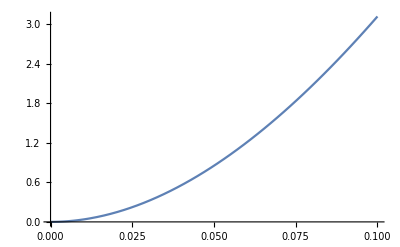

{{x→0.0543855}}

```mathematica
Plot[Interpolation[tempdata][x],{x,0,0.1}]
NSolve[Interpolation[tempdata][x]==1,x]//Quiet
```

## CDR (width subchannel WW)

```mathematica
higgsprecepc=Table[If[i==4||i==8||i==9||i==11,higgsprecepcoriginal[[i]],Infinity],{i,1,11}]
```

{∞,∞,∞,0.0098,∞,∞,∞,0.003068,0.029991,∞,0.005}

```mathematica
higgsobscepc[kz_,kw_,kg_,kgamma_,kb_,kt_,ktau_]:={kz^2 ktau^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 ktau^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kgamma^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kw^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^4/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kg^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kt^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kb^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kw^2 kb^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],6/7 kz^2 kb^2/kh[kz,kw,kg,kgamma,kb,kt,ktau]+1/7 kw^2 kb^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2};
chisquarecepc[{kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_},lumif_]:=Sum[((higgsobscepc[kz,kw,kg,kgamma,kb,kt,ktau][[i]]-1)/higgsprecepc[[i]])((higgsobscepc[kz,kw,kg,kgamma,kb,kt,ktau][[j]]-1)/higgsprecepc[[j]])inputcorrelations[[i,j]]/100/lumif,{i,1,Length[higgsprecepc]},{j,1,Length[higgsprecepc]}]
higgsobsLHCratios[kz_,kw_,kg_,kgamma_,kb_,kt_,ktau_]:={kg^2 kz^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kgamma/kz,kw/kz,kb/kz,ktau/kz,kg/kz,kt/kg,ktau/kz};
higgspreLHCratiosL={2.0/100,1.8/100,2.1/100,7.4/100,7.8/100,4.5/100,5.0/100,6.1/100};
(*higgspreLHCratiosH={5.7/100,2.6/100,3.1/100,9.8/100,8.9/100,8.7/100,8/100,9.4/100,6.3/100};*)
chisquarecepcL[{kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_},lumif_]:=Sum[((higgsobscepc[kz,kw,kg,kgamma,kb,kt,ktau][[i]]-1)/higgsprecepc[[i]])((higgsobscepc[kz,kw,kg,kgamma,kb,kt,ktau][[j]]-1)/higgsprecepc[[j]])inputcorrelations[[i,j]]/100/lumif,{i,1,Length[higgsprecepc]},{j,1,Length[higgsprecepc]}]+Sum[(higgsobsLHCratios[kz,kw,kg,kgamma,kb,kt,ktau][[i]]-1)^2/higgspreLHCratiosL[[i]]^2,{i,1,Length[higgspreLHCratiosL]}]
```

```mathematica
higgsobscepc10p[kz_,kw_,kg_,kgamma_,kb_,kt_,ktau_,kmu_,brinv_,ktotal_]:={kz^2 kmu^2/ktotal,kz^2 ktau^2/ktotal,kz^2 kgamma^2/ktotal,kz^2 kw^2/ktotal,kz^4/ktotal,kz^2 kg^2/ktotal,kz^2 kt^2/ktotal,kz^2 kb^2/ktotal,kw^2 kb^2/ktotal,6/7 kz^2 kb^2/ktotal+1/7 kw^2 kb^2/ktotal,kz^2,kz^2brinv+1};
chisquarecepc10p[{kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_,kmu_,brinv_,ktotal_},lumif_]:=Sum[((higgsobscepc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[i]]-1)/higgsprecepc[[i]])((higgsobscepc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[j]]-1)/higgsprecepc[[j]])inputcorrelations[[i,j]]/100/lumif,{i,1,Length[higgsprecepc]},{j,1,Length[higgsprecepc]}]+(higgsobscepc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[-1]]-1)^2/higgsobscepcinv^2
```

```mathematica
func=chisquarecepc10p[{kb,kt,kg,kw,ktau,kz,kgamma,kmu,0,ktotal},1]
```

0.+1111.78 (-1+(kb^2 kw^2)/ktotal)^2+40000. (-1+kz^2)^2-10478.4 (-1+(kb^2 kw^2)/ktotal) (-1+(kb^2 kz^2)/ktotal)+106240. (-1+(kb^2 kz^2)/ktotal)^2-31.8463 (-1+(kb^2 kw^2)/ktotal) (-1+(kw^2 kz^2)/ktotal)+645.239 (-1+(kb^2 kz^2)/ktotal) (-1+(kw^2 kz^2)/ktotal)+10412.3 (-1+(kw^2 kz^2)/ktotal)^2

```mathematica
func/.ktotal->1+x;
tempdata=Table[{x,NMinimize[{%,0<kz<2,0<kw<2,0<kb<2},{kz,kw,kb}][[1]]},{x,-0.1,0.1,0.002}]
```

{{-0.1,8.0851},{-0.098,7.76173},{-0.096,7.44509},{-0.094,7.13516},{-0.092,6.83194},{-0.09,6.53541},{-0.088,6.24558},{-0.086,5.96243},{-0.084,5.68595},{-0.082,5.41615},{-0.08,5.153},{-0.078,4.89652},{-0.076,4.64667},{-0.074,4.40347},{-0.072,4.16689},{-0.07,3.93694},{-0.068,3.71361},{-0.066,3.49689},{-0.064,3.28676},{-0.062,3.08323},{-0.06,2.88628},{-0.058,2.69591},{-0.056,2.51211},{-0.054,2.33487},{-0.052,2.16419},{-0.05,2.00004},{-0.048,1.84244},{-0.046,1.69137},{-0.044,1.54682},{-0.042,1.40878},{-0.04,1.27724},{-0.038,1.15221},{-0.036,1.03366},{-0.034,0.921593},{-0.032,0.816},{-0.03,0.716871},{-0.028,0.624198},{-0.026,0.537973},{-0.024,0.458188},{-0.022,0.384834},{-0.02,0.317903},{-0.018,0.257386},{-0.016,0.203276},{-0.014,0.155563},{-0.012,0.11424},{-0.01,0.0792977},{-0.008,0.0507277},{-0.006,0.0285214},{-0.004,0.0126705},{-0.002,0.00316618},{0.,1.63667×10^-21},{0.002,0.00316331},{0.004,0.0126475},{0.006,0.0284438},{0.008,0.0505437},{0.01,0.0789384},{0.012,0.113619},{0.014,0.154577},{0.016,0.201804},{0.018,0.25529},{0.02,0.315028},{0.022,0.381008},{0.024,0.453221},{0.026,0.531658},{0.028,0.616311},{0.03,0.707171},{0.032,0.804228},{0.034,0.907474},{0.036,1.0169},{0.038,1.1325},{0.04,1.25426},{0.042,1.38217},{0.044,1.51622},{0.046,1.65641},{0.048,1.80273},{0.05,1.95516},{0.052,2.1137},{0.054,2.27834},{0.056,2.44907},{0.058,2.62588},{0.06,2.80876},{0.062,2.9977},{0.064,3.19269},{0.066,3.39373},{0.068,3.6008},{0.07,3.81389},{0.072,4.03301},{0.074,4.25812},{0.076,4.48924},{0.078,4.72634},{0.08,4.96942},{0.082,5.21848},{0.084,5.47349},{0.086,5.73445},{0.088,6.00135},{0.09,6.27418},{0.092,6.55294},{0.094,6.83761},{0.096,7.12818},{0.098,7.42465},{0.1,7.72701}}

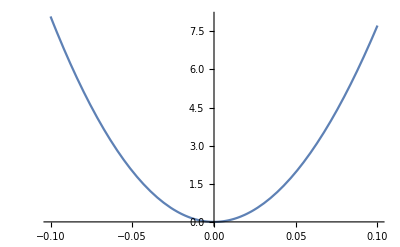

{{x→0.0356983}}

```mathematica
Plot[Interpolation[tempdata][x],{x,-0.1,0.1}]
NSolve[Interpolation[tempdata][x]==1,x]//Quiet
```